### Linear waves in a plucked string with tied ends. The string is symmetric and has a central region and two lateral regions with propagation velocity c_p and c_c, respectively. We place the x-axis along the string. Then, the central region is given by -x_p<=x<=x_p and the two lateral regions are given by -x_c<=x<=-x_p and x_p<=x<=x_c. In each region, the perturbed velocity is of the form: v[x] = A Cos[k x] + B Sin[k x], where k = ω/c; c stands for c_p and c_c. Since the string is symmetric and the wave equation is symmetric, too, the function v[x] is either even or odd about x = 0. This symmetry condition is imposed with the help of the logical variable EvenParity.

```mathematica
ClearAll["Global`*"]
```

#### General solutions in the three regions.

```mathematica
(*vclgen[x_]=Subscript[A, 1] Exp[ⅈ ω x/Subscript[c, c]]+Subscript[B, 1] Exp[-ⅈ ω x/Subscript[c, c]]
vcrgen[x_]=Subscript[A, 3] Exp[ⅈ ω x/Subscript[c, c]]+Subscript[B, 3] Exp[-ⅈ ω x/Subscript[c, c]]*)
vclgen[x_]=Subscript[A, 1] Cos[ω x/Subscript[c, c]]+Subscript[B, 1] Sin[ ω x/Subscript[c, c]]
vpgen[x_]=Subscript[A, 2] Cos[ω x/Subscript[c, p]]+Subscript[B, 2] Sin[ ω x/Subscript[c, p]]
vcrgen[x_]=Subscript[A, 3] Cos[ω x/Subscript[c, c]]+Subscript[B, 3] Sin[ ω x/Subscript[c, c]]
```

Cos[(x ω)/c_c] A_1+Sin[(x ω)/c_c] B_1

Cos[(x ω)/c_p] A_2+Sin[(x ω)/c_p] B_2

Cos[(x ω)/c_c] A_3+Sin[(x ω)/c_c] B_3

#### Solutions in the three regions for the selected parity.

```mathematica
EvenParity=True;
If[EvenParity,
(
Print["v[x] is even"];
vcl[x_]=vclgen[x]/.{Subscript[A, 1]->A,Subscript[B, 1]->-B};
vp[x_]=C Cos[ω x/Subscript[c, p]];
vcr[x_]=vcrgen[x]/.{Subscript[A, 3]->A,Subscript[B, 3]->B};
),
(
Print["v[x] is odd"];
vcl[x_]=vclgen[x]/.{Subscript[A, 1]->-A,Subscript[B, 1]->B};
vp[x_]=C Sin[ω x/Subscript[c, p]];
vcr[x_]=vcrgen[x]/.{Subscript[A, 3]->A,Subscript[B, 3]->B};
)]
vcl[x]
vp[x]
vcr[x]
```

v[x] is even

A Cos[(x ω)/c_c]-B Sin[(x ω)/c_c]

C Cos[(x ω)/c_p]

A Cos[(x ω)/c_c]+B Sin[(x ω)/c_c]

#### We impose that the velocity and its x-derivative are continuous at x=x_p and that it vanishes at x=x_c. Because of parity, the velocity automatically vanishes at x=-x_c.

```mathematica
eqn1=vcr[Subscript[x, c]]
eqn2=vp[Subscript[x, p]]-vcr[Subscript[x, p]]
eqn3=vp'[Subscript[x, p]]-vcr'[Subscript[x, p]]
```

A Cos[(ω x_c)/c_c]+B Sin[(ω x_c)/c_c]

-A Cos[(ω x_p)/c_c]+C Cos[(ω x_p)/c_p]-B Sin[(ω x_p)/c_c]

-(B ω Cos[(ω x_p)/c_c])/c_c+(A ω Sin[(ω x_p)/c_c])/c_c-(C ω Sin[(ω x_p)/c_p])/c_p

#### Matrix of the system of the three equations.

```mathematica
eqns={eqn1,eqn2,eqn3}
{b,m}=CoefficientArrays[eqns,{A,B,C}];
MatrixForm[m]
```

{A Cos[(ω x_c)/c_c]+B Sin[(ω x_c)/c_c],-A Cos[(ω x_p)/c_c]+C Cos[(ω x_p)/c_p]-B Sin[(ω x_p)/c_c],-(B ω Cos[(ω x_p)/c_c])/c_c+(A ω Sin[(ω x_p)/c_c])/c_c-(C ω Sin[(ω x_p)/c_p])/c_p}

(Cos[(ω x_c)/c_c] | Sin[(ω x_c)/c_c] | 0
-Cos[(ω x_p)/c_c] | -Sin[(ω x_p)/c_c] | Cos[(ω x_p)/c_p]
(ω Sin[(ω x_p)/c_c])/c_c | -(ω Cos[(ω x_p)/c_c])/c_c | -(ω Sin[(ω x_p)/c_p])/c_p)

#### The determinant of the system gives us the dispersion relation. It must be zero for the system to have a solution other than A = B = C = 0.

```mathematica
dr=Simplify[Det[m]/ω]
(*dr=Simplify[ExpToTrig[Det[m]]]*)
```

(Cos[(ω (x_c-x_p))/c_c] Cos[(ω x_p)/c_p])/c_c-(Sin[(ω (x_c-x_p))/c_c] Sin[(ω x_p)/c_p])/c_p

#### Now, the rank of the system is two, which means that we must impose the value of one of the three constants and calculate the other two in terms of the first one. We use the second and third equations to get A and B in terms of C. We also check that this solution satisfies the first equation.

```mathematica
solAB=Solve[{eqn2==0,eqn3==0},{A,B}];
solAB=Simplify[solAB]
{Asol}=A/.solAB
{Bsol}=B/.solAB
(*solABtrig=ExpToTrig[solAB]
{Asol}=ComplexExpand[Re[A/.solABtrig]]
{Bsol}=ComplexExpand[Re[B/.solABtrig]]*)
Print["Equation eqn1 is satisfied:"]
Simplify[eqn1/.{A->Asol,B->Bsol}];
%==Expand[C Subscript[c, c] dr]
```

{{A→C Cos[(ω x_p)/c_c] Cos[(ω x_p)/c_p]+(C Sin[(ω x_p)/c_c] Sin[(ω x_p)/c_p] c_c)/c_p,B→C Cos[(ω x_p)/c_p] Sin[(ω x_p)/c_c]-(C Cos[(ω x_p)/c_c] Sin[(ω x_p)/c_p] c_c)/c_p}}

{C Cos[(ω x_p)/c_c] Cos[(ω x_p)/c_p]+(C Sin[(ω x_p)/c_c] Sin[(ω x_p)/c_p] c_c)/c_p}

{C Cos[(ω x_p)/c_p] Sin[(ω x_p)/c_c]-(C Cos[(ω x_p)/c_c] Sin[(ω x_p)/c_p] c_c)/c_p}

Equation eqn1 is satisfied:

True

#### From this point we work with numerical values of the parameters.

```mathematica
repl={C->1,Subscript[x, p]->0.1,Subscript[x, c]->1,Subscript[c, p]->1,Subscript[c, c]->Sqrt[6]}
```

{C→1,x_p→0.1,x_c→1,c_p→1,c_c→√6}

#### Approximate values of the frequencies from Joarder & Roberts (1992). They work well if x_p<<x_c.

```mathematica
n={1,2,3,4}
If[EvenParity,
(Print["Hybrid mode"];
ωh=Subscript[c, p]/Sqrt[Subscript[x, p](Subscript[x, c]-Subscript[x, p])]/.repl
),
Indeterminate
]
Print["Internal modes"]
If[EvenParity,ωi=(n π Subscript[c, p])/Subscript[x, p]/.repl,ωi=((n-1/2) π Subscript[c, p])/Subscript[x, p]/.repl]
Print["External modes"]
ωe=(n π Subscript[c, c])/(Subscript[x, c]-Subscript[x, p])/.repl
```

{1,2,3,4}

Hybrid mode

3.33333

Internal modes

{31.4159,62.8319,94.2478,125.664}

External modes

{8.55033,17.1007,25.651,34.2013}

#### Plot the dispersion relation versus ω and the approximate values of the frequency.

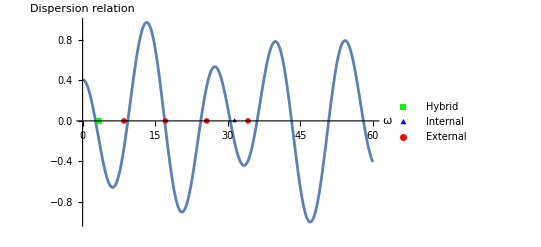

```mathematica
plt1=Plot[dr/.repl,{ω,0,60},AxesLabel->{"ω","Dispersion relation"}];
(*Show[plt1,GridLines->{{ωh},{}}]*)
data=Table[{ωi[[n]],0},{n,1,Length[ωi]}];
plti=ListPlot[data,PlotStyle->{Blue},PlotMarkers->{▲,10},PlotLegends->LineLegend[{"Internal"}]];
data=Table[{ωe[[n]],0},{n,1,Length[ωe]}];
plte=ListPlot[data,PlotStyle->{Red},PlotMarkers->{●,10},PlotLegends->LineLegend[{"External"}]];
If[EvenParity,plth=ListPlot[{{ωh,0}},PlotStyle->{Green},PlotMarkers->{■,10},PlotLegends->LineLegend[{"Hybrid"}]];
Show[plt1,plth,plti,plte]
,
Show[plt1,plti,plte]
]
```

#### One solution to the dispersion relation is computed numerically and the corresponding velocity is plotted.

Guess value of the frequency:

30

{ω→30.5174}

{A→-0.109648,B→-1.01402}

Piecewise[{{-0.109648 Cos[12.4587 x]+1.01402 Sin[12.4587 x], x<-0.1}, {Cos[30.5174 x], Abs[x]≤0.1}, {-0.109648 Cos[12.4587 x]-1.01402 Sin[12.4587 x], x>0.1}, {0, True}}]

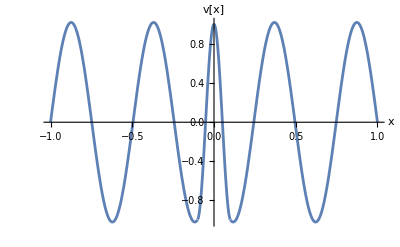

```mathematica
Print["Guess value of the frequency:"]
ω0=30
replω=FindRoot[(dr/.repl)==0,{ω,ω0}]
replAB={A->Asol/.repl/.replω,B->Bsol/.repl/.replω}
v[x_]=Piecewise[{{vcl[x],x<-Subscript[x, p]},{vp[x],Abs[x]<=Subscript[x, p]},{vcr[x],x>Subscript[x, p]}}]/.repl/.replω/.replAB
Plot[v[x],{x,-Subscript[x, c]/.repl,Subscript[x, c]/.repl},AxesLabel->{"x","v[x]"}]
```